```mathematica
SetDirectory[NotebookDirectory[]];
fns=FileNames["1064_USAF_CAL_take3-2021-03-09-154847.png"]
camdata=ImageData[Import[#],"Byte"]&/@fns;
(*camdata=Table[ImageData[ImageRotate[Image[camdata[[i]],"Byte"],π/180*13+π/2],"Byte"],{i,1,17}];*)
```

{1064_USAF_CAL_take3-2021-03-09-154847.png}

```mathematica
Gaussian[A_,x_,y_,wx_,wy_]:=A Exp[-x^2/wx^2-y^2/wy^2]
```

```mathematica
data3D=Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,camdata[[1]],{2}],1]
```

{{1,1,65},{1,2,148},{1,3,26},{1,4,241},{1,5,24},{1,6,19},{1,7,20},{1,8,19},{1,9,18},{1,10,17},{1,11,15},{1,12,19},{1,13,20},{1,14,20},{1,15,19},{1,16,20},{1,17,18},{1,18,25},{1,19,20},{1,20,20},{1,21,23},{1,22,21},{1,23,16},{1,24,21},{1,25,17},1228750,{960,1256,26},{960,1257,16},{960,1258,17},{960,1259,17},{960,1260,24},{960,1261,27},{960,1262,10},{960,1263,16},{960,1264,13},{960,1265,31},{960,1266,24},{960,1267,18},{960,1268,35},{960,1269,24},{960,1270,16},{960,1271,18},{960,1272,16},{960,1273,21},{960,1274,21},{960,1275,12},{960,1276,19},{960,1277,15},{960,1278,17},{960,1279,14},{960,1280,22}}
 |  |  |  |

```mathematica
Print[Dimensions[data3D]]
```

{1228800,3}

```mathematica
Print[Show[
Image[camdata[[1]],"Byte"],ImageSize->1000
]];
```

-Graphics-

```mathematica
nlmf = NonlinearModelFit[data3D,{A0 Exp[-2(((x-x0)/ωx0)^2+((y-(960-y0))/ωy0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2+((y-(960-y1))/ωy1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2+((y-(960-y2))/ωy2)^2)]+b},{{x0,320},{y0,362},{ωx0,10},{ωy0,10},{A0,200},{x1,320},{y1,310},{ωx1,10},{ωy1,10},{A1,200},{x2,320},{y2,260},{ωx2,10},{ωy2,10},{A2,200},{b,0}},{y,x}]
%["ParameterTable"]
```

```mathematica
FittedModel[84.60410851663231+245.5734141923697 ⅇ^(-2 («1»))+247.24781539055402 ⅇ^(«1»)+246.948361534553 ⅇ^(-2 (0.00014497802829415685 («1»)^2+«21» «1»))]
```

General::munfl: Exp[-2281.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1757.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1464.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 317.83 | 0.411774 | 771.856 | 0.
y0 | 360.054 | 0.111326 | 3234.23 | 0.
ωx0 | 83.0518 | 0.824543 | 100.725 | 0.
ωy0 | 22.3535 | 0.225591 | 99.0886 | 0.
A0 | 246.948 | 2.45449 | 100.611 | 0.
x1 | 320.038 | 0.413169 | 774.593 | 0.
y1 | 307.581 | 0.110958 | 2772.05 | 0.
ωx1 | 83.0986 | 0.827323 | 100.443 | 0.
ωy1 | 22.1617 | 0.226754 | 97.7344 | 0.
A1 | 247.248 | 2.46867 | 100.154 | 0.
x2 | 322.34 | 0.429065 | 751.262 | 0.
y2 | 255.296 | 0.107871 | 2366.68 | 0.
ωx2 | 83.6619 | 0.859112 | 97.3819 | 0.
ωy2 | 20.9722 | 0.217725 | 96.324 | 0.
A2 | 245.573 | 2.52283 | 97.3404 | 0.
b | 84.6041 | 0.0604416 | 1399.77 | 0.

```mathematica
data3D[[961]]
```

{1,961,51}

{960}

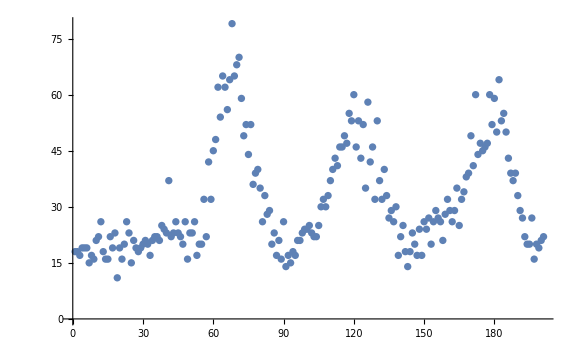

```mathematica
Test = {};
For[i=1,i≤ 960*1280,i++,If[data3D[[i]][[2]] ==800,AppendTo[Test,data3D[[i]][[3]]]]]
Print[Dimensions[Test]]
ListPlot[Test[[300;;500]],ImageSize->Large]
```

```mathematica
Clear[x,b]
```

```mathematica
nlmf = NonlinearModelFit[Test[[300;;500]],{A0 Exp[-2(((x-x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2)]+b},{{x0,70},{ωx0,10},{A0,200},{x1,120},{ωx1,10},{A1,200},{x2,180},{ωx2,10},{A2,200},{b,0}},{x}]
%["ParameterTable"]
```

FittedModel[20.1279+34.8249 ⅇ^(-0.00657981 (-«19»+x)^2)+32.1062 ⅇ^(-0.00609603 («1»)^2)+48.0451 ⅇ^(-0.0108585 (-68.3085+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 68.3085 | 0.282643 | 241.678 | 1.84748×10^-239
ωx0 | 13.5715 | 0.609883 | 22.2527 | 6.15854×10^-55
A0 | 48.0451 | 1.78063 | 26.982 | 4.48308×10^-67
x1 | 120.7 | 0.488629 | 247.017 | 2.88321×10^-241
ωx1 | 18.113 | 1.07805 | 16.8016 | 1.71886×10^-39
A1 | 32.1062 | 1.55532 | 20.6428 | 1.57895×10^-50
x2 | 178.086 | 0.442238 | 402.692 | 1.00274×10^-281
ωx2 | 17.4344 | 0.967203 | 18.0256 | 4.43313×10^-43
A2 | 34.8249 | 1.58951 | 21.9092 | 5.2323×10^-54
b | 20.1279 | 0.575776 | 34.9579 | 6.17347×10^-85

```mathematica
72.639-120.191
```

-47.552

```mathematica
120.191 - 177.137
```

-56.946

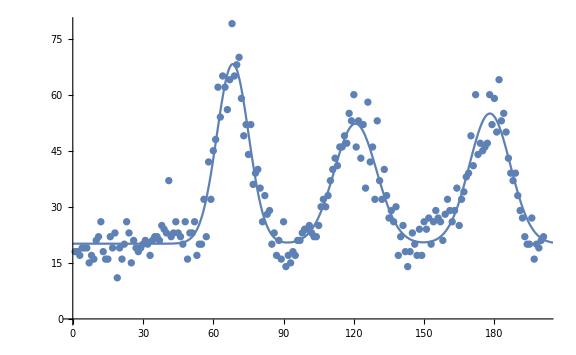

```mathematica
Show[{ListPlot[Test[[300;;500]],ImageSize->Large],Plot[{nlmf[x]},{x,0,300},PlotRange->All]}]
```

```mathematica
(*228.1 line pairs per mm for G7E6--so each line pair is 1/228.1 from center to center*)
1/228.1
((120.7-68.308)+(178-120.7))/2
```

0.00438404

54.846

```mathematica
(*54.846 pixels is 4.384 µm so 12.51 pixels/µm *)
```

{960}

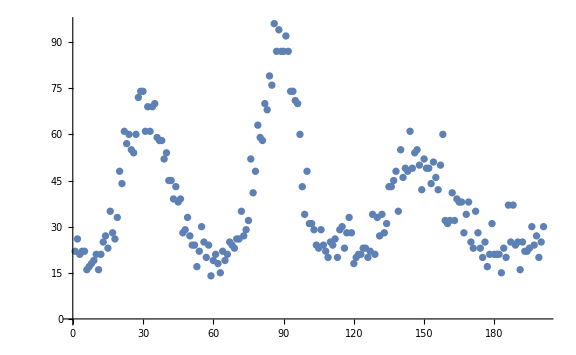

```mathematica
Test = {};
For[i=1,i≤ 960*1280,i++,If[data3D[[i]][[2]] ==684,AppendTo[Test,data3D[[i]][[3]]]]]
Print[Dimensions[Test]]
ListPlot[Test[[300;;500]],ImageSize->Large]
```

```mathematica
Clear[x,b]
```

```mathematica
nlmf = NonlinearModelFit[Test[[300;;500]],{A0 Exp[-2(((x-x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2)]+b},{{x0,40},{ωx0,10},{A0,200},{x1,90},{ωx1,10},{A1,200},{x2,150},{ωx2,10},{A2,200},{b,0}},{x}]
%["ParameterTable"]
```

FittedModel[21.9809+30.0107 ⅇ^(-0.00361211 (-«19»+x)^2)+69.1684 ⅇ^(-0.00944522 ((«1»«1»)^2)+47.9014 ⅇ^(-0.00700475 (-31.4312+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 31.4312 | 0.350036 | 89.7941 | 3.65782×10^-158
ωx0 | 16.8974 | 0.788416 | 21.432 | 1.04649×10^-52
A0 | 47.9014 | 1.79515 | 26.6838 | 2.40591×10^-66
x1 | 88.2727 | 0.224959 | 392.395 | 1.40337×10^-279
ωx1 | 14.5515 | 0.498431 | 29.1947 | 2.419×10^-72
A1 | 69.1684 | 1.92403 | 35.9498 | 5.94729×10^-87
x2 | 148.498 | 0.659317 | 225.23 | 1.23795×10^-233
ωx2 | 23.5307 | 1.54379 | 15.2421 | 7.6029×10^-35
A2 | 30.0107 | 1.54653 | 19.4051 | 4.78002×10^-47
b | 21.9809 | 0.729979 | 30.1117 | 1.87837×10^-74

```mathematica
72.639-120.191
```

-47.552

```mathematica
120.191 - 177.137
```

-56.946

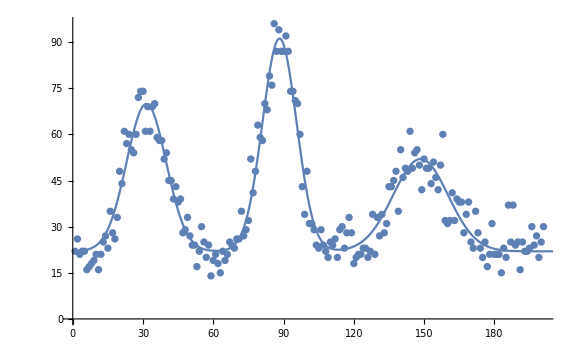

```mathematica
Show[{ListPlot[Test[[300;;500]],ImageSize->Large],Plot[{nlmf[x]},{x,0,300},PlotRange->All]}]
```

```mathematica
(*203.2 line pairs per mm for G7E5--so each line pair is 1/203.2 from center to center*)
1/203.2
((88.27-31.4)+(148.498-88.27))/2
```

0.00492126

58.549

```mathematica
(*so 58.549 pixels is 4.9212 µm, which is 11.90 pixels/µm*)
```

{960}

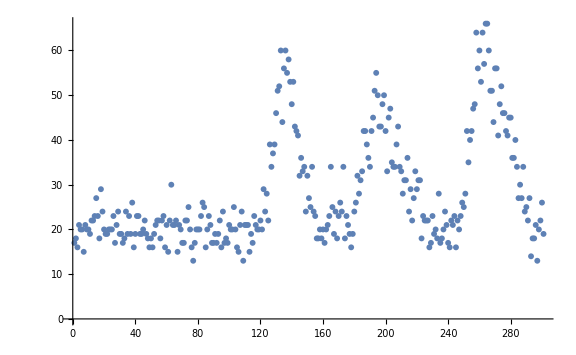

```mathematica
Test = {};
For[i=1,i≤ 960*1280,i++,If[data3D[[i]][[2]] ==476,AppendTo[Test,data3D[[i]][[3]]]]]
Print[Dimensions[Test]]
ListPlot[Test[[150;;450]],ImageSize->Large]
```

```mathematica
Clear[x,b]
```

```mathematica
nlmf = NonlinearModelFit[Test[[150;;450]],{A0 Exp[-2(((x-x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2)]+b},{{x0,140},{ωx0,10},{A0,200},{x1,200},{ωx1,10},{A1,200},{x2,280},{ωx2,10},{A2,200},{b,0}},{x}]
%["ParameterTable"]
```

FittedModel[19.9991+39.268 ⅇ^(-0.00442754 (-«19»+x)^2)+25.6792 ⅇ^(-0.00392688 («1»)^2)+36.1306 ⅇ^(-0.00954705 (-136.414+x)^2)]

General::munfl: Exp[-916.707] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-860.633] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1079.49] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 136.414 | 0.346558 | 393.624 | 0.
ωx0 | 14.4737 | 0.72239 | 20.0359 | 1.01868×10^-56
A0 | 36.1306 | 1.52024 | 23.7663 | 3.91283×10^-70
x1 | 197.575 | 0.608874 | 324.492 | 0.
ωx1 | 22.5679 | 1.29595 | 17.4141 | 4.98888×10^-47
A1 | 25.6792 | 1.22753 | 20.9194 | 6.04874×10^-60
x2 | 266.28 | 0.386409 | 689.116 | 0.
ωx2 | 21.2537 | 0.819079 | 25.9482 | 1.09598×10^-77
A2 | 39.268 | 1.26368 | 31.0744 | 1.94417×10^-94
b | 19.9991 | 0.361351 | 55.3455 | 1.63655×10^-156

```mathematica
72.639-120.191
```

-47.552

```mathematica
120.191 - 177.137
```

-56.946

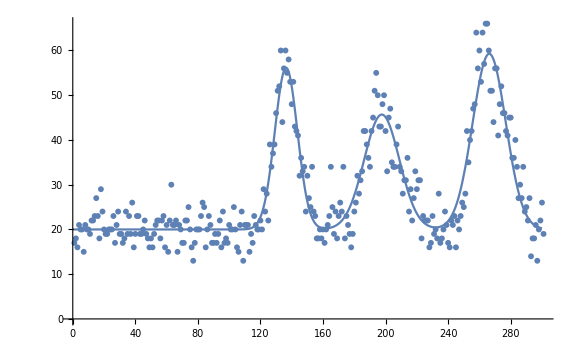

```mathematica
Show[{ListPlot[Test[[150;;450]],ImageSize->Large],Plot[{nlmf[x]},{x,0,300},PlotRange->All]}]
```

```mathematica
(*181.0 line pairs per mm for G7E4--so each line pair is 1/181.0 from center to center*)
1/181.0
((197.575-136.414)+(266.28-197.575))/2
```

0.00552486

64.933

```mathematica
(*so 64.933 pixels is 5.52 µm, which is 11.76 pixels/µm*)


(*so averaged:*)
```

```mathematica
(12.5+11.9+11.76)/3
```

12.0533